```mathematica
Needs["Notation`"];
Notation[𝓊 ⟺ cu]
Notation[𝒿 ⟺ cj]
```

```mathematica
<<sneg`sneg`;
snegfermionoperators[a,b,c];
snegrealconstants[cj,cu,U1,t,t11,t12,cd,x];
```

sneg 1.250 Copyright (C) 2016 Rok Zitko

```mathematica
myop = {a[1],a[2],a[3],a[4]}
```

{a^,a[2],a[3],a[4]}

```mathematica
makebasis[myop]
```

{a_(1⇑)^†,a_(1↓)^†,a_(2⇑)^†,a_(2↓)^†,a_(3⇑)^†,a_(3↓)^†,a_(4⇑)^†,a_(4↓)^†}

```mathematica
vc4 = qszbasisvc[myop]
```

{{{-4,0},{‖▯▯▯▯▯▯▯▯⟩}},{{-3,-1/2},{‖▯▯▯▯▯▯▯▮⟩,‖▯▯▯▯▯▮▯▯⟩,‖▯▯▯▮▯▯▯▯⟩,‖▯▮▯▯▯▯▯▯⟩}},{{-3,1/2},{‖▯▯▯▯▯▯▮▯⟩,‖▯▯▯▯▮▯▯▯⟩,‖▯▯▮▯▯▯▯▯⟩,‖▮▯▯▯▯▯▯▯⟩}},{{-2,-1},{‖▯▯▯▯▯▮▯▮⟩,‖▯▯▯▮▯▯▯▮⟩,‖▯▯▯▮▯▮▯▯⟩,‖▯▮▯▯▯▯▯▮⟩,‖▯▮▯▯▯▮▯▯⟩,‖▯▮▯▮▯▯▯▯⟩}},{{-2,0},{‖▯▯▯▯▯▯▮▮⟩,‖▯▯▯▯▯▮▮▯⟩,‖▯▯▯▯▮▯▯▮⟩,‖▯▯▯▯▮▮▯▯⟩,‖▯▯▯▮▯▯▮▯⟩,‖▯▯▯▮▮▯▯▯⟩,‖▯▯▮▯▯▯▯▮⟩,‖▯▯▮▯▯▮▯▯⟩,‖▯▯▮▮▯▯▯▯⟩,‖▯▮▯▯▯▯▮▯⟩,‖▯▮▯▯▮▯▯▯⟩,‖▯▮▮▯▯▯▯▯⟩,‖▮▯▯▯▯▯▯▮⟩,‖▮▯▯▯▯▮▯▯⟩,‖▮▯▯▮▯▯▯▯⟩,‖▮▮▯▯▯▯▯▯⟩}},{{-2,1},{‖▯▯▯▯▮▯▮▯⟩,‖▯▯▮▯▯▯▮▯⟩,‖▯▯▮▯▮▯▯▯⟩,‖▮▯▯▯▯▯▮▯⟩,‖▮▯▯▯▮▯▯▯⟩,‖▮▯▮▯▯▯▯▯⟩}},{{-1,-3/2},{‖▯▯▯▮▯▮▯▮⟩,‖▯▮▯▯▯▮▯▮⟩,‖▯▮▯▮▯▯▯▮⟩,‖▯▮▯▮▯▮▯▯⟩}},{{-1,-1/2},{‖▯▯▯▯▯▮▮▮⟩,‖▯▯▯▯▮▮▯▮⟩,‖▯▯▯▮▯▯▮▮⟩,‖▯▯▯▮▯▮▮▯⟩,‖▯▯▯▮▮▯▯▮⟩,‖▯▯▯▮▮▮▯▯⟩,‖▯▯▮▯▯▮▯▮⟩,‖▯▯▮▮▯▯▯▮⟩,‖▯▯▮▮▯▮▯▯⟩,‖▯▮▯▯▯▯▮▮⟩,‖▯▮▯▯▯▮▮▯⟩,‖▯▮▯▯▮▯▯▮⟩,‖▯▮▯▯▮▮▯▯⟩,‖▯▮▯▮▯▯▮▯⟩,‖▯▮▯▮▮▯▯▯⟩,‖▯▮▮▯▯▯▯▮⟩,‖▯▮▮▯▯▮▯▯⟩,‖▯▮▮▮▯▯▯▯⟩,‖▮▯▯▯▯▮▯▮⟩,‖▮▯▯▮▯▯▯▮⟩,‖▮▯▯▮▯▮▯▯⟩,‖▮▮▯▯▯▯▯▮⟩,‖▮▮▯▯▯▮▯▯⟩,‖▮▮▯▮▯▯▯▯⟩}},{{-1,1/2},{‖▯▯▯▯▮▯▮▮⟩,‖▯▯▯▯▮▮▮▯⟩,‖▯▯▯▮▮▯▮▯⟩,‖▯▯▮▯▯▯▮▮⟩,‖▯▯▮▯▯▮▮▯⟩,‖▯▯▮▯▮▯▯▮⟩,‖▯▯▮▯▮▮▯▯⟩,‖▯▯▮▮▯▯▮▯⟩,‖▯▯▮▮▮▯▯▯⟩,‖▯▮▯▯▮▯▮▯⟩,‖▯▮▮▯▯▯▮▯⟩,‖▯▮▮▯▮▯▯▯⟩,‖▮▯▯▯▯▯▮▮⟩,‖▮▯▯▯▯▮▮▯⟩,‖▮▯▯▯▮▯▯▮⟩,‖▮▯▯▯▮▮▯▯⟩,‖▮▯▯▮▯▯▮▯⟩,‖▮▯▯▮▮▯▯▯⟩,‖▮▯▮▯▯▯▯▮⟩,‖▮▯▮▯▯▮▯▯⟩,‖▮▯▮▮▯▯▯▯⟩,‖▮▮▯▯▯▯▮▯⟩,‖▮▮▯▯▮▯▯▯⟩,‖▮▮▮▯▯▯▯▯⟩}},{{-1,3/2},{‖▯▯▮▯▮▯▮▯⟩,‖▮▯▯▯▮▯▮▯⟩,‖▮▯▮▯▯▯▮▯⟩,‖▮▯▮▯▮▯▯▯⟩}},{{0,-2},{‖▯▮▯▮▯▮▯▮⟩}},{{0,-1},{‖▯▯▯▮▯▮▮▮⟩,‖▯▯▯▮▮▮▯▮⟩,‖▯▯▮▮▯▮▯▮⟩,‖▯▮▯▯▯▮▮▮⟩,‖▯▮▯▯▮▮▯▮⟩,‖▯▮▯▮▯▯▮▮⟩,‖▯▮▯▮▯▮▮▯⟩,‖▯▮▯▮▮▯▯▮⟩,‖▯▮▯▮▮▮▯▯⟩,‖▯▮▮▯▯▮▯▮⟩,‖▯▮▮▮▯▯▯▮⟩,‖▯▮▮▮▯▮▯▯⟩,‖▮▯▯▮▯▮▯▮⟩,‖▮▮▯▯▯▮▯▮⟩,‖▮▮▯▮▯▯▯▮⟩,‖▮▮▯▮▯▮▯▯⟩}},{{0,0},{‖▯▯▯▯▮▮▮▮⟩,‖▯▯▯▮▮▯▮▮⟩,‖▯▯▯▮▮▮▮▯⟩,‖▯▯▮▯▯▮▮▮⟩,‖▯▯▮▯▮▮▯▮⟩,‖▯▯▮▮▯▯▮▮⟩,‖▯▯▮▮▯▮▮▯⟩,‖▯▯▮▮▮▯▯▮⟩,‖▯▯▮▮▮▮▯▯⟩,‖▯▮▯▯▮▯▮▮⟩,‖▯▮▯▯▮▮▮▯⟩,‖▯▮▯▮▮▯▮▯⟩,‖▯▮▮▯▯▯▮▮⟩,‖▯▮▮▯▯▮▮▯⟩,‖▯▮▮▯▮▯▯▮⟩,‖▯▮▮▯▮▮▯▯⟩,‖▯▮▮▮▯▯▮▯⟩,‖▯▮▮▮▮▯▯▯⟩,‖▮▯▯▯▯▮▮▮⟩,‖▮▯▯▯▮▮▯▮⟩,‖▮▯▯▮▯▯▮▮⟩,‖▮▯▯▮▯▮▮▯⟩,‖▮▯▯▮▮▯▯▮⟩,‖▮▯▯▮▮▮▯▯⟩,‖▮▯▮▯▯▮▯▮⟩,‖▮▯▮▮▯▯▯▮⟩,‖▮▯▮▮▯▮▯▯⟩,‖▮▮▯▯▯▯▮▮⟩,‖▮▮▯▯▯▮▮▯⟩,‖▮▮▯▯▮▯▯▮⟩,‖▮▮▯▯▮▮▯▯⟩,‖▮▮▯▮▯▯▮▯⟩,‖▮▮▯▮▮▯▯▯⟩,‖▮▮▮▯▯▯▯▮⟩,‖▮▮▮▯▯▮▯▯⟩,‖▮▮▮▮▯▯▯▯⟩}},{{0,1},{‖▯▯▮▯▮▯▮▮⟩,‖▯▯▮▯▮▮▮▯⟩,‖▯▯▮▮▮▯▮▯⟩,‖▯▮▮▯▮▯▮▯⟩,‖▮▯▯▯▮▯▮▮⟩,‖▮▯▯▯▮▮▮▯⟩,‖▮▯▯▮▮▯▮▯⟩,‖▮▯▮▯▯▯▮▮⟩,‖▮▯▮▯▯▮▮▯⟩,‖▮▯▮▯▮▯▯▮⟩,‖▮▯▮▯▮▮▯▯⟩,‖▮▯▮▮▯▯▮▯⟩,‖▮▯▮▮▮▯▯▯⟩,‖▮▮▯▯▮▯▮▯⟩,‖▮▮▮▯▯▯▮▯⟩,‖▮▮▮▯▮▯▯▯⟩}},{{0,2},{‖▮▯▮▯▮▯▮▯⟩}},{{1,-3/2},{‖▯▮▯▮▯▮▮▮⟩,‖▯▮▯▮▮▮▯▮⟩,‖▯▮▮▮▯▮▯▮⟩,‖▮▮▯▮▯▮▯▮⟩}},{{1,-1/2},{‖▯▯▯▮▮▮▮▮⟩,‖▯▯▮▮▯▮▮▮⟩,‖▯▯▮▮▮▮▯▮⟩,‖▯▮▯▯▮▮▮▮⟩,‖▯▮▯▮▮▯▮▮⟩,‖▯▮▯▮▮▮▮▯⟩,‖▯▮▮▯▯▮▮▮⟩,‖▯▮▮▯▮▮▯▮⟩,‖▯▮▮▮▯▯▮▮⟩,‖▯▮▮▮▯▮▮▯⟩,‖▯▮▮▮▮▯▯▮⟩,‖▯▮▮▮▮▮▯▯⟩,‖▮▯▯▮▯▮▮▮⟩,‖▮▯▯▮▮▮▯▮⟩,‖▮▯▮▮▯▮▯▮⟩,‖▮▮▯▯▯▮▮▮⟩,‖▮▮▯▯▮▮▯▮⟩,‖▮▮▯▮▯▯▮▮⟩,‖▮▮▯▮▯▮▮▯⟩,‖▮▮▯▮▮▯▯▮⟩,‖▮▮▯▮▮▮▯▯⟩,‖▮▮▮▯▯▮▯▮⟩,‖▮▮▮▮▯▯▯▮⟩,‖▮▮▮▮▯▮▯▯⟩}},{{1,1/2},{‖▯▯▮▯▮▮▮▮⟩,‖▯▯▮▮▮▯▮▮⟩,‖▯▯▮▮▮▮▮▯⟩,‖▯▮▮▯▮▯▮▮⟩,‖▯▮▮▯▮▮▮▯⟩,‖▯▮▮▮▮▯▮▯⟩,‖▮▯▯▯▮▮▮▮⟩,‖▮▯▯▮▮▯▮▮⟩,‖▮▯▯▮▮▮▮▯⟩,‖▮▯▮▯▯▮▮▮⟩,‖▮▯▮▯▮▮▯▮⟩,‖▮▯▮▮▯▯▮▮⟩,‖▮▯▮▮▯▮▮▯⟩,‖▮▯▮▮▮▯▯▮⟩,‖▮▯▮▮▮▮▯▯⟩,‖▮▮▯▯▮▯▮▮⟩,‖▮▮▯▯▮▮▮▯⟩,‖▮▮▯▮▮▯▮▯⟩,‖▮▮▮▯▯▯▮▮⟩,‖▮▮▮▯▯▮▮▯⟩,‖▮▮▮▯▮▯▯▮⟩,‖▮▮▮▯▮▮▯▯⟩,‖▮▮▮▮▯▯▮▯⟩,‖▮▮▮▮▮▯▯▯⟩}},{{1,3/2},{‖▮▯▮▯▮▯▮▮⟩,‖▮▯▮▯▮▮▮▯⟩,‖▮▯▮▮▮▯▮▯⟩,‖▮▮▮▯▮▯▮▯⟩}},{{2,-1},{‖▯▮▯▮▮▮▮▮⟩,‖▯▮▮▮▯▮▮▮⟩,‖▯▮▮▮▮▮▯▮⟩,‖▮▮▯▮▯▮▮▮⟩,‖▮▮▯▮▮▮▯▮⟩,‖▮▮▮▮▯▮▯▮⟩}},{{2,0},{‖▯▯▮▮▮▮▮▮⟩,‖▯▮▮▯▮▮▮▮⟩,‖▯▮▮▮▮▯▮▮⟩,‖▯▮▮▮▮▮▮▯⟩,‖▮▯▯▮▮▮▮▮⟩,‖▮▯▮▮▯▮▮▮⟩,‖▮▯▮▮▮▮▯▮⟩,‖▮▮▯▯▮▮▮▮⟩,‖▮▮▯▮▮▯▮▮⟩,‖▮▮▯▮▮▮▮▯⟩,‖▮▮▮▯▯▮▮▮⟩,‖▮▮▮▯▮▮▯▮⟩,‖▮▮▮▮▯▯▮▮⟩,‖▮▮▮▮▯▮▮▯⟩,‖▮▮▮▮▮▯▯▮⟩,‖▮▮▮▮▮▮▯▯⟩}},{{2,1},{‖▮▯▮▯▮▮▮▮⟩,‖▮▯▮▮▮▯▮▮⟩,‖▮▯▮▮▮▮▮▯⟩,‖▮▮▮▯▮▯▮▮⟩,‖▮▮▮▯▮▮▮▯⟩,‖▮▮▮▮▮▯▮▯⟩}},{{3,-1/2},{‖▯▮▮▮▮▮▮▮⟩,‖▮▮▯▮▮▮▮▮⟩,‖▮▮▮▮▯▮▮▮⟩,‖▮▮▮▮▮▮▯▮⟩}},{{3,1/2},{‖▮▯▮▮▮▮▮▮⟩,‖▮▮▮▯▮▮▮▮⟩,‖▮▮▮▮▮▯▮▮⟩,‖▮▮▮▮▮▮▮▯⟩}},{{4,0},{‖▮▮▮▮▮▮▮▮⟩}}}

```mathematica
basisp2 = Select[vc4,#[[1]]=={0,2}&][[1,2]]
```

{‖▮▯▮▯▮▯▮▯⟩}

```mathematica
basisp1 = Select[vc4,#[[1]]=={0,1}&][[1,2]]
```

{‖▯▯▮▯▮▯▮▮⟩,‖▯▯▮▯▮▮▮▯⟩,‖▯▯▮▮▮▯▮▯⟩,‖▯▮▮▯▮▯▮▯⟩,‖▮▯▯▯▮▯▮▮⟩,‖▮▯▯▯▮▮▮▯⟩,‖▮▯▯▮▮▯▮▯⟩,‖▮▯▮▯▯▯▮▮⟩,‖▮▯▮▯▯▮▮▯⟩,‖▮▯▮▯▮▯▯▮⟩,‖▮▯▮▯▮▮▯▯⟩,‖▮▯▮▮▯▯▮▯⟩,‖▮▯▮▮▮▯▯▯⟩,‖▮▮▯▯▮▯▮▯⟩,‖▮▮▮▯▯▯▮▯⟩,‖▮▮▮▯▮▯▯▯⟩}

```mathematica
basis00 = Select[vc4,#[[1]]=={0,0}&][[1,2]]
```

{‖▯▯▯▯▮▮▮▮⟩,‖▯▯▯▮▮▯▮▮⟩,‖▯▯▯▮▮▮▮▯⟩,‖▯▯▮▯▯▮▮▮⟩,‖▯▯▮▯▮▮▯▮⟩,‖▯▯▮▮▯▯▮▮⟩,‖▯▯▮▮▯▮▮▯⟩,‖▯▯▮▮▮▯▯▮⟩,‖▯▯▮▮▮▮▯▯⟩,‖▯▮▯▯▮▯▮▮⟩,‖▯▮▯▯▮▮▮▯⟩,‖▯▮▯▮▮▯▮▯⟩,‖▯▮▮▯▯▯▮▮⟩,‖▯▮▮▯▯▮▮▯⟩,‖▯▮▮▯▮▯▯▮⟩,‖▯▮▮▯▮▮▯▯⟩,‖▯▮▮▮▯▯▮▯⟩,‖▯▮▮▮▮▯▯▯⟩,‖▮▯▯▯▯▮▮▮⟩,‖▮▯▯▯▮▮▯▮⟩,‖▮▯▯▮▯▯▮▮⟩,‖▮▯▯▮▯▮▮▯⟩,‖▮▯▯▮▮▯▯▮⟩,‖▮▯▯▮▮▮▯▯⟩,‖▮▯▮▯▯▮▯▮⟩,‖▮▯▮▮▯▯▯▮⟩,‖▮▯▮▮▯▮▯▯⟩,‖▮▮▯▯▯▯▮▮⟩,‖▮▮▯▯▯▮▮▯⟩,‖▮▮▯▯▮▯▯▮⟩,‖▮▮▯▯▮▮▯▯⟩,‖▮▮▯▮▯▯▮▯⟩,‖▮▮▯▮▮▯▯▯⟩,‖▮▮▮▯▯▯▯▮⟩,‖▮▮▮▯▯▮▯▯⟩,‖▮▮▮▮▯▯▯▯⟩}

```mathematica
basisn1 = Select[vc4,#[[1]]=={0,-1}&][[1,2]]
```

{‖▯▯▯▮▯▮▮▮⟩,‖▯▯▯▮▮▮▯▮⟩,‖▯▯▮▮▯▮▯▮⟩,‖▯▮▯▯▯▮▮▮⟩,‖▯▮▯▯▮▮▯▮⟩,‖▯▮▯▮▯▯▮▮⟩,‖▯▮▯▮▯▮▮▯⟩,‖▯▮▯▮▮▯▯▮⟩,‖▯▮▯▮▮▮▯▯⟩,‖▯▮▮▯▯▮▯▮⟩,‖▯▮▮▮▯▯▯▮⟩,‖▯▮▮▮▯▮▯▯⟩,‖▮▯▯▮▯▮▯▮⟩,‖▮▮▯▯▯▮▯▮⟩,‖▮▮▯▮▯▯▯▮⟩,‖▮▮▯▮▯▮▯▯⟩}

```mathematica
basisn2 = Select[vc4,#[[1]]=={0,-2}&][[1,2]]
```

{‖▯▮▯▮▯▮▯▮⟩}

```mathematica
basis00//Dimensions
```

{36}

```mathematica
basisp1//Dimensions
```

{16}

```mathematica
1+16+36+1+16
```

70

```mathematica
hhop = -t11(hop[a[1],a[3]]+hop[a[2],a[4]])-t12(hop[a[1],a[4]]+hop[a[2],a[3]])
```

-t12 (a_(1↓)^†·a_(4↓)^+a_(1⇑)^†·a_(4⇑)^+a_(2↓)^†·a_(3↓)^+a_(2⇑)^†·a_(3⇑)^+a_(3↓)^†·a_(2↓)^+a_(3⇑)^†·a_(2⇑)^+a_(4↓)^†·a_(1↓)^+a_(4⇑)^†·a_(1⇑)^)-t11 (a_(1↓)^†·a_(3↓)^+a_(1⇑)^†·a_(3⇑)^+a_(2↓)^†·a_(4↓)^+a_(2⇑)^†·a_(4⇑)^+a_(3↓)^†·a_(1↓)^+a_(3⇑)^†·a_(1⇑)^+a_(4↓)^†·a_(2↓)^+a_(4⇑)^†·a_(2⇑)^)

```mathematica
hhU = cu(hubbard[a[1]]+hubbard[a[2]]+hubbard[a[3]]+hubbard[a[4]])
```

𝓊 (-(a_(1↓)^†·a_(1⇑)^†·a_(1↓)^·a_(1⇑)^)-a_(2↓)^†·a_(2⇑)^†·a_(2↓)^·a_(2⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(3↓)^·a_(3⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(4↓)^·a_(4⇑)^)

```mathematica
hhu1 = (cu-2cj)(nc[number[a[1],UP],number[a[2],DO]]+nc[number[a[1],DO],number[a[2],UP]]+nc[number[a[3],UP],number[a[4],DO]]+nc[number[a[3],DO],number[a[4],UP]])//Simplify
```

(2 𝒿-𝓊) (a_(1↓)^†·a_(2⇑)^†·a_(1↓)^·a_(2⇑)^+a_(1⇑)^†·a_(2↓)^†·a_(1⇑)^·a_(2↓)^+a_(3↓)^†·a_(4⇑)^†·a_(3↓)^·a_(4⇑)^+a_(3⇑)^†·a_(4↓)^†·a_(3⇑)^·a_(4↓)^)

```mathematica
hhj1 = (cu-3cj)(nc[number[a[1],UP],number[a[2],UP]]+nc[number[a[1],DO],number[a[2],DO]]+nc[number[a[3],UP],number[a[4],UP]]+nc[number[a[3],DO],number[a[4],DO]])
```

(-3 𝒿+𝓊) (-(a_(1↓)^†·a_(2↓)^†·a_(1↓)^·a_(2↓)^)-a_(1⇑)^†·a_(2⇑)^†·a_(1⇑)^·a_(2⇑)^-a_(3↓)^†·a_(4↓)^†·a_(3↓)^·a_(4↓)^-a_(3⇑)^†·a_(4⇑)^†·a_(3⇑)^·a_(4⇑)^)

```mathematica
hhpj1 = nc[a[CR,1,UP],a[AN,1,DO],a[CR,2,DO],a[AN,2,UP]]+nc[a[CR,3,UP],a[AN,3,DO],a[CR,4,DO],a[AN,4,UP]]
```

-(a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^)-a_(3⇑)^†·a_(4↓)^†·a_(3↓)^·a_(4⇑)^

```mathematica
hhpj = (-cj)(conj[hhpj1]+hhpj1)
```

-𝒿 (-(a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^)-a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^-a_(3↓)^†·a_(4⇑)^†·a_(3⇑)^·a_(4↓)^-a_(3⇑)^†·a_(4↓)^†·a_(3↓)^·a_(4⇑)^)

```mathematica
hfj1 = nc[a[CR,1,UP],a[AN,2,UP],a[CR,1,DO],a[AN,2,DO]]+nc[a[CR,3,UP],a[AN,4,UP],a[CR,3,DO],a[AN,4,DO]]
```

-(a_(1↓)^†·a_(1⇑)^†·a_(2↓)^·a_(2⇑)^)-a_(3↓)^†·a_(3⇑)^†·a_(4↓)^·a_(4⇑)^

```mathematica
hhfj = (-cj)(conj[hfj1]+hfj1)
```

-𝒿 (-(a_(1↓)^†·a_(1⇑)^†·a_(2↓)^·a_(2⇑)^)-a_(2↓)^†·a_(2⇑)^†·a_(1↓)^·a_(1⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(4↓)^·a_(4⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(3↓)^·a_(3⇑)^)

```mathematica
ham = hhop+ hhU +hhu1 + hhj1+ hhpj+hhfj//Simplify
```

-t12 (a_(1↓)^†·a_(4↓)^+a_(1⇑)^†·a_(4⇑)^+a_(2↓)^†·a_(3↓)^+a_(2⇑)^†·a_(3⇑)^+a_(3↓)^†·a_(2↓)^+a_(3⇑)^†·a_(2⇑)^+a_(4↓)^†·a_(1↓)^+a_(4⇑)^†·a_(1⇑)^)-t11 (a_(1↓)^†·a_(3↓)^+a_(1⇑)^†·a_(3⇑)^+a_(2↓)^†·a_(4↓)^+a_(2⇑)^†·a_(4⇑)^+a_(3↓)^†·a_(1↓)^+a_(3⇑)^†·a_(1⇑)^+a_(4↓)^†·a_(2↓)^+a_(4⇑)^†·a_(2⇑)^)+𝒿 (a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^+a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^+a_(3↓)^†·a_(4⇑)^†·a_(3⇑)^·a_(4↓)^+a_(3⇑)^†·a_(4↓)^†·a_(3↓)^·a_(4⇑)^)+(2 𝒿-𝓊) (a_(1↓)^†·a_(2⇑)^†·a_(1↓)^·a_(2⇑)^+a_(1⇑)^†·a_(2↓)^†·a_(1⇑)^·a_(2↓)^+a_(3↓)^†·a_(4⇑)^†·a_(3↓)^·a_(4⇑)^+a_(3⇑)^†·a_(4↓)^†·a_(3⇑)^·a_(4↓)^)+(3 𝒿-𝓊) (a_(1↓)^†·a_(2↓)^†·a_(1↓)^·a_(2↓)^+a_(1⇑)^†·a_(2⇑)^†·a_(1⇑)^·a_(2⇑)^+a_(3↓)^†·a_(4↓)^†·a_(3↓)^·a_(4↓)^+a_(3⇑)^†·a_(4⇑)^†·a_(3⇑)^·a_(4⇑)^)+𝒿 (a_(1↓)^†·a_(1⇑)^†·a_(2↓)^·a_(2⇑)^+a_(2↓)^†·a_(2⇑)^†·a_(1↓)^·a_(1⇑)^+a_(3↓)^†·a_(3⇑)^†·a_(4↓)^·a_(4⇑)^+a_(4↓)^†·a_(4⇑)^†·a_(3↓)^·a_(3⇑)^)-𝓊 (a_(1↓)^†·a_(1⇑)^†·a_(1↓)^·a_(1⇑)^+a_(2↓)^†·a_(2⇑)^†·a_(2↓)^·a_(2⇑)^+a_(3↓)^†·a_(3⇑)^†·a_(3↓)^·a_(3⇑)^+a_(4↓)^†·a_(4⇑)^†·a_(4↓)^·a_(4⇑)^)

```mathematica
mybasis = {basisp2,basisp1,basis00,basisn1,basisn2}//Flatten
```

{‖▮▯▮▯▮▯▮▯⟩,‖▯▯▮▯▮▯▮▮⟩,‖▯▯▮▯▮▮▮▯⟩,‖▯▯▮▮▮▯▮▯⟩,‖▯▮▮▯▮▯▮▯⟩,‖▮▯▯▯▮▯▮▮⟩,‖▮▯▯▯▮▮▮▯⟩,‖▮▯▯▮▮▯▮▯⟩,‖▮▯▮▯▯▯▮▮⟩,‖▮▯▮▯▯▮▮▯⟩,‖▮▯▮▯▮▯▯▮⟩,‖▮▯▮▯▮▮▯▯⟩,‖▮▯▮▮▯▯▮▯⟩,‖▮▯▮▮▮▯▯▯⟩,‖▮▮▯▯▮▯▮▯⟩,‖▮▮▮▯▯▯▮▯⟩,‖▮▮▮▯▮▯▯▯⟩,‖▯▯▯▯▮▮▮▮⟩,‖▯▯▯▮▮▯▮▮⟩,‖▯▯▯▮▮▮▮▯⟩,‖▯▯▮▯▯▮▮▮⟩,‖▯▯▮▯▮▮▯▮⟩,‖▯▯▮▮▯▯▮▮⟩,‖▯▯▮▮▯▮▮▯⟩,‖▯▯▮▮▮▯▯▮⟩,‖▯▯▮▮▮▮▯▯⟩,‖▯▮▯▯▮▯▮▮⟩,‖▯▮▯▯▮▮▮▯⟩,‖▯▮▯▮▮▯▮▯⟩,‖▯▮▮▯▯▯▮▮⟩,‖▯▮▮▯▯▮▮▯⟩,‖▯▮▮▯▮▯▯▮⟩,‖▯▮▮▯▮▮▯▯⟩,‖▯▮▮▮▯▯▮▯⟩,‖▯▮▮▮▮▯▯▯⟩,‖▮▯▯▯▯▮▮▮⟩,‖▮▯▯▯▮▮▯▮⟩,‖▮▯▯▮▯▯▮▮⟩,‖▮▯▯▮▯▮▮▯⟩,‖▮▯▯▮▮▯▯▮⟩,‖▮▯▯▮▮▮▯▯⟩,‖▮▯▮▯▯▮▯▮⟩,‖▮▯▮▮▯▯▯▮⟩,‖▮▯▮▮▯▮▯▯⟩,‖▮▮▯▯▯▯▮▮⟩,‖▮▮▯▯▯▮▮▯⟩,‖▮▮▯▯▮▯▯▮⟩,‖▮▮▯▯▮▮▯▯⟩,‖▮▮▯▮▯▯▮▯⟩,‖▮▮▯▮▮▯▯▯⟩,‖▮▮▮▯▯▯▯▮⟩,‖▮▮▮▯▯▮▯▯⟩,‖▮▮▮▮▯▯▯▯⟩,‖▯▯▯▮▯▮▮▮⟩,‖▯▯▯▮▮▮▯▮⟩,‖▯▯▮▮▯▮▯▮⟩,‖▯▮▯▯▯▮▮▮⟩,‖▯▮▯▯▮▮▯▮⟩,‖▯▮▯▮▯▯▮▮⟩,‖▯▮▯▮▯▮▮▯⟩,‖▯▮▯▮▮▯▯▮⟩,‖▯▮▯▮▮▮▯▯⟩,‖▯▮▮▯▯▮▯▮⟩,‖▯▮▮▮▯▯▯▮⟩,‖▯▮▮▮▯▮▯▯⟩,‖▮▯▯▮▯▮▯▮⟩,‖▮▮▯▯▯▮▯▮⟩,‖▮▮▯▮▯▯▯▮⟩,‖▮▮▯▮▯▮▯▯⟩,‖▯▮▯▮▯▮▯▮⟩}

```mathematica
mybasis//Dimensions
```

{70}

```mathematica
basis00//Dimensions
```

{36}

```mathematica
td = {cj->cu/5,cu->6,t12->x t11,t11->0.3}
```

{𝒿→𝓊/5,𝓊→6,t12→t11 x,t11→0.3}

```mathematica
mymat=matrixrepresentationop[ham,mybasis]//.td
```

{{24/5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,12,0,-0.3,0.3 x,0,0,0,0.3,0,-0.3 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,12,0.3 x,-0.3,0,0,0,0,0.3,0,0.3 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-0.3,0.3 x,42/5,0,0,0,0,0,0,0,0,-0.3,0.3 x,-6/5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0.3 x,-0.3,0,6,0,0,-6/5,0,0,0,0,0,0,0,-0.3,0.3 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,12,0,-0.3,-0.3 x,0,0.3,0,0,0,-0.3 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,12,0.3 x,0,-0.3 x,0,-0.3,0,0,0.3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,-6/5,-0.3,0.3 x,6,0,0,0,0,0.3 x,-0.3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0.3,0,0,0,-0.3 x,0,0,42/5,0,0,-6/5,0.3,0,0,-0.3 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0.3,0,0,0,-0.3 x,0,0,6,-6/5,0,-0.3 x,0,0,0.3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-0.3 x,0,0,0,0.3,0,0,0,-6/5,6,0,0,0.3,0,0,-0.3 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0.3 x,0,0,0,-0.3,0,-6/5,0,0,42/5,0,0.3 x,0,0,-0.3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-0.3,0,0,0,0.3 x,0.3,-0.3 x,0,0,12,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0.3 x,0,0,0,-0.3,0,0,0.3,0.3 x,0,12,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-6/5,0,-0.3 x,0.3,0,0,0,0,0,0,0,42/5,-0.3 x,0.3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,-0.3,0,0,0,-0.3 x,0.3,0,0,0,0,-0.3 x,12,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0.3 x,0,0,0,0,0,-0.3 x,-0.3,0,0,0.3,0,12,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,24,0.3 x,0.3,-0.3 x,-0.3,0,0,0,0,0.3,0.3 x,0,0,0,0,0,0,0,-0.3,-0.3 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.3 x,12,0,0,0,0.3 x,0,-0.3,0,0,0,0.3 x,0,0,0,0,0,0,0,0,0.3,0,-0.3 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.3,0,12,0,0,0,0.3 x,0,0.3,0,0,-0.3,0,0,0,0,0,0,0,0,0,0.3,0,0.3 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.3 x,0,0,12,0,-0.3 x,-0.3,0,0,0,0,0,0.3,0.3 x,0,0,0,0,0,0,0,0,0,0,-0.3 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.3,0,0,0,12,0,0,0.3 x,-0.3,0,0,0,0,0,-0.3,0.3 x,0,0,0,0,0,0,0,0,0.3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.3 x,0,-0.3 x,0,12,0,0,-6/5,0,0,0,0,0,0,0,0.3 x,0,0,0,0,0,0,0,0,-0.3 x,0,-6/5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.3 x,-0.3,0,0,48/5,-6/5,0,0,0,0,0,0,0,0,-0.3,0,0,0,0,0,0,0,0,0,0.3 x,0,-6/5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.3,0,0,0.3 x,0,-6/5,48/5,0,0,0,0,0,0,0,0,0,0.3 x,0,0,0,0,0,0,0,-0.3,0,0,0,-6/5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.3,0,-0.3,-6/5,0,0,12,0,0,0,0,0,0,0,0,0.3,0,0,0,0,0,0,0,0,-0.3,0,0,0,-6/5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.3,0,0,0,0,0,0,0,0,12,0,-0.3,-0.3 x,0,0.3,0,0,0,0,0,0,0,0,0,0,0,0,0.3,0,-0.3 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.3 x,0,0,0,0,0,0,0,0,0,12,0.3 x,0,-0.3 x,0,-0.3,0,0,0,0,0,0,0,0,0,0,0,0,0.3,0,0.3 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.3 x,-0.3,0,0,0,0,0,0,-0.3,0.3 x,24/5,0,0,0,0,0.3 x,-0.3,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.3,0.3 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.3,0,0,0,0,0,-0.3 x,0,0,48/5,0,0,-6/5,0.3,0,0,0,-6/5,0,0,0,0,0,0,0,0,0,0,0,0,-0.3 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.3 x,0,0,0,0,0,0,-0.3 x,0,0,36/5,-6/5,0,-0.3 x,0,0,0,0,-6/5,0,0,0,0,0,0,0,0,0,0,0,0,0.3 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.3,0,0,0,0,0.3,0,0,0,-6/5,36/5,0,0,0.3,0,0,0,0,-6/5,0,0,0,0,0,0,0,0,0,0,-0.3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.3 x,0,0,0,0,0,-0.3,0,-6/5,0,0,48/5,0,0.3 x,0,0,0,0,0,-6/5,0,0,0,0,0,0,0,0,0,0,-0.3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.3 x,-0.3,0,0,0,0,0.3 x,0.3,-0.3 x,0,0,12,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.3 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.3 x,0.3,0,0,-0.3,0,0,0.3,0.3 x,0,12,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,12,0,-0.3 x,-0.3,0,0,0.3,0,0,-0.3,-0.3 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.3 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,12,0,0,0.3 x,-0.3,-0.3 x,0,0,0,0,0.3,-0.3 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.3,0,0,0,0,0,0,0,0,0,0,-6/5,0,0,0,0,0,-0.3 x,0,48/5,0,0,-6/5,0,0.3,0,0,0,0,0,-0.3 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.3,0,0,0,0,0,0,0,0,0,0,-6/5,0,0,0,0,-0.3,0,0,36/5,-6/5,0,0,0,-0.3,0,0,0,0,0.3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.3 x,0,0,0,0,0,0,0,0,0,0,0,0,-6/5,0,0,0,0,0.3 x,0,-6/5,36/5,0,0,0.3 x,0,0,0,0,0,0,-0.3 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.3 x,0,0,0,0,0,0,0,0,0,0,0,0,-6/5,0,0,0,-0.3,-6/5,0,0,48/5,0,0,0.3 x,0,0,0,0,0,-0.3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.3 x,0.3,0,0,0,0,0,0,0,0,0,0,0,0,0,0.3,-0.3 x,0,0,0,0,24/5,-0.3 x,0.3,0,0,0,0,0,0,0.3,-0.3 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.3 x,0,-0.3,0,0,0,0,0,0,0,0,0,0,0,0,0.3,0,0.3 x,0,-0.3 x,12,0,0,0,0,0,0,0,0,0,-0.3 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.3 x,0,-0.3,0,0,0,0,0,0,0,0,0,0,0,0,-0.3,0,0.3 x,0.3,0,12,0,0,0,0,0,0,0,0,-0.3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-6/5,0,0,0,0.3,0,0,0,0,0,0,0,0,-0.3,0,0,0,0,0,0,0,0,12,0,0,-6/5,0.3,0,-0.3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-6/5,0,0,0,0.3,0,0,0,0,0,0,0,-0.3 x,0,0,0,0,0,0,0,0,0,48/5,-6/5,0,-0.3 x,0,0,0.3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-6/5,0,-0.3 x,0,0,0,0,0,0,0,0,0,0.3,0,0,0,0,0,0,0,0,-6/5,48/5,0,0,0.3,-0.3 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-6/5,0,0.3 x,0,0,0,0,0,0,0,0,-0.3 x,0,0,0,0,0,0,0,-6/5,0,0,12,0,0.3 x,0,-0.3 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.3,0,0,0,0,0,0,0,0,-0.3 x,0.3,0,0,0,0,0,0.3,-0.3 x,0,0,12,0,0,0,0.3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.3 x,0,0,0,0,0,0,0,0,0,0,-0.3 x,-0.3,0,0,0,0,0,0.3,0.3 x,0,12,0,0,0.3 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.3 x,0,-0.3,0,0,0,0,0,0,0,0,0,0.3,0,0,-0.3,0,-0.3 x,0,0,0,12,0,-0.3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.3 x,0,-0.3,0,0,0,0,0,0,0,0,-0.3 x,0,0,0,0.3,0,-0.3 x,0,0,0,12,-0.3 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.3 x,0.3,0,0,0,0,0,0,0,-0.3 x,-0.3,0,0,0,0,0.3,0.3 x,-0.3,-0.3 x,24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,12,0,-0.3,0,0,0.3,0.3 x,0,0,0,0,0,-0.3 x,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,12,0.3 x,0,0,0,0,-0.3,0.3 x,0,0,0,0.3,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.3,0.3 x,42/5,0,0,0,0,0,0,0,-0.3,0.3 x,0,-6/5,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,12,0,-0.3 x,-0.3,0,0,0.3,0,0,0,-0.3 x,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,12,0,0,0.3 x,-0.3,-0.3 x,0,0,0,0.3,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.3,0,0,-0.3 x,0,42/5,0,0,-6/5,0,0.3,0,0,0,-0.3 x,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.3 x,0,0,-0.3,0,0,6,-6/5,0,0,0,-0.3,0,0,0,0.3 x,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.3,0,0,0.3 x,0,-6/5,6,0,0,0.3 x,0,0,0,-0.3,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.3 x,0,0,-0.3,-6/5,0,0,42/5,0,0,0.3 x,0,0,0,-0.3,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.3,-0.3 x,0,0,0,0,6,-0.3 x,0.3,-6/5,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.3,0,0,0.3,0,0.3 x,0,-0.3 x,12,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.3 x,0,0,0,-0.3,0,0.3 x,0.3,0,12,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.3 x,0.3,0,0,0,0,0,0,0,-6/5,0,0,6,0,0.3,-0.3 x,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-6/5,-0.3 x,0.3,0,0,0,0,0,0,0,0,42/5,-0.3 x,0.3,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.3 x,0,-0.3,0,0,0,0,0.3,-0.3 x,12,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.3 x,0,-0.3,0,0,0,-0.3 x,0.3,0,12,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,24/5}}

```mathematica
mymat//Dimensions
```

{70,70}

```mathematica
vals1=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[1]]},{xx,0,2,0.1}];
vals2=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[2]]},{xx,0,2,0.1}];
vals3=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[3]]},{xx,0,2,0.1}];
```

```mathematica
vals4=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[4]]},{xx,0,2,0.1}];
```

```mathematica
vals5=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[5]]},{xx,0,2,0.1}];
```

```mathematica
vals6=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[6]]},{xx,0,2,0.1}];
```

```mathematica
vals7=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[7]]},{xx,0,2,0.1}];
```

```mathematica
vals8=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[8]]},{xx,0,2,0.1}];
```

```mathematica
vals9=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[9]]},{xx,0,2,0.1}];
```

```mathematica
vals10=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[10]]},{xx,0,2,0.1}];
```

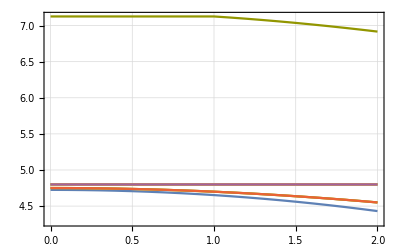

```mathematica
ListLinePlot[{vals1,vals2,vals3,vals4,vals5,vals6,vals7,vals8,vals9,vals10},Frame->True,GridLines->Automatic,PlotRange->All]
```

```mathematica
Expand[(a1+a2+a3+a4)(a1+a2+a3+a4)]
```

a1^2+2 a1 a2+a2^2+2 a1 a3+2 a2 a3+a3^2+2 a1 a4+2 a2 a4+2 a3 a4+a4^2

```mathematica
S2 = spinspin[a[1],a[1]]+2spinspin[a[1],a[2]]+spinspin[a[2],a[2]]+2spinspin[a[1],a[3]]+2spinspin[a[2],a[3]]+spinspin[a[3],a[3]]+2spinspin[a[1],a[4]]+2spinspin[a[2],a[4]]+2spinspin[a[3],a[4]]+spinspin[a[4],a[4]]//Simplify
```

1/4 (3 a_(1↓)^†·a_(1↓)^+3 a_(1⇑)^†·a_(1⇑)^+3 a_(2↓)^†·a_(2↓)^+3 a_(2⇑)^†·a_(2⇑)^+3 a_(3↓)^†·a_(3↓)^+3 a_(3⇑)^†·a_(3⇑)^+3 a_(4↓)^†·a_(4↓)^+3 a_(4⇑)^†·a_(4⇑)^+6 a_(1↓)^†·a_(1⇑)^†·a_(1↓)^·a_(1⇑)^-2 a_(1↓)^†·a_(2↓)^†·a_(1↓)^·a_(2↓)^+2 a_(1↓)^†·a_(2⇑)^†·a_(1↓)^·a_(2⇑)^-4 a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^-2 a_(1↓)^†·a_(3↓)^†·a_(1↓)^·a_(3↓)^+2 a_(1↓)^†·a_(3⇑)^†·a_(1↓)^·a_(3⇑)^-4 a_(1↓)^†·a_(3⇑)^†·a_(1⇑)^·a_(3↓)^-2 a_(1↓)^†·a_(4↓)^†·a_(1↓)^·a_(4↓)^+2 a_(1↓)^†·a_(4⇑)^†·a_(1↓)^·a_(4⇑)^-4 a_(1↓)^†·a_(4⇑)^†·a_(1⇑)^·a_(4↓)^-4 a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^+2 a_(1⇑)^†·a_(2↓)^†·a_(1⇑)^·a_(2↓)^-2 a_(1⇑)^†·a_(2⇑)^†·a_(1⇑)^·a_(2⇑)^-4 a_(1⇑)^†·a_(3↓)^†·a_(1↓)^·a_(3⇑)^+2 a_(1⇑)^†·a_(3↓)^†·a_(1⇑)^·a_(3↓)^-2 a_(1⇑)^†·a_(3⇑)^†·a_(1⇑)^·a_(3⇑)^-4 a_(1⇑)^†·a_(4↓)^†·a_(1↓)^·a_(4⇑)^+2 a_(1⇑)^†·a_(4↓)^†·a_(1⇑)^·a_(4↓)^-2 a_(1⇑)^†·a_(4⇑)^†·a_(1⇑)^·a_(4⇑)^+6 a_(2↓)^†·a_(2⇑)^†·a_(2↓)^·a_(2⇑)^-2 a_(2↓)^†·a_(3↓)^†·a_(2↓)^·a_(3↓)^+2 a_(2↓)^†·a_(3⇑)^†·a_(2↓)^·a_(3⇑)^-4 a_(2↓)^†·a_(3⇑)^†·a_(2⇑)^·a_(3↓)^-2 a_(2↓)^†·a_(4↓)^†·a_(2↓)^·a_(4↓)^+2 a_(2↓)^†·a_(4⇑)^†·a_(2↓)^·a_(4⇑)^-4 a_(2↓)^†·a_(4⇑)^†·a_(2⇑)^·a_(4↓)^-4 a_(2⇑)^†·a_(3↓)^†·a_(2↓)^·a_(3⇑)^+2 a_(2⇑)^†·a_(3↓)^†·a_(2⇑)^·a_(3↓)^-2 a_(2⇑)^†·a_(3⇑)^†·a_(2⇑)^·a_(3⇑)^-4 a_(2⇑)^†·a_(4↓)^†·a_(2↓)^·a_(4⇑)^+2 a_(2⇑)^†·a_(4↓)^†·a_(2⇑)^·a_(4↓)^-2 a_(2⇑)^†·a_(4⇑)^†·a_(2⇑)^·a_(4⇑)^+6 a_(3↓)^†·a_(3⇑)^†·a_(3↓)^·a_(3⇑)^-2 a_(3↓)^†·a_(4↓)^†·a_(3↓)^·a_(4↓)^+2 a_(3↓)^†·a_(4⇑)^†·a_(3↓)^·a_(4⇑)^-4 a_(3↓)^†·a_(4⇑)^†·a_(3⇑)^·a_(4↓)^-4 a_(3⇑)^†·a_(4↓)^†·a_(3↓)^·a_(4⇑)^+2 a_(3⇑)^†·a_(4↓)^†·a_(3⇑)^·a_(4↓)^-2 a_(3⇑)^†·a_(4⇑)^†·a_(3⇑)^·a_(4⇑)^+6 a_(4↓)^†·a_(4⇑)^†·a_(4↓)^·a_(4⇑)^)

```mathematica
Clear[avs2];
data1={};
Do[
Do[pos1=(Position[Eigensystem[mymat/.x->xx1][[1]],Sort[Eigensystem[mymat/.x->xx1][[1]]][[j]]]//Flatten)[[1]];
e1=Sort[Eigensystem[mymat/.x->xx1][[1]]][[j]];
wf1=Eigensystem[mymat/.x->xx1][[2,pos1]];
fullwf1=Sum[wf1[[i]]mybasis[[i]],{i,1,Dimensions[mybasis][[1]]}];
avs2=(matrixrepresentationop[S2,{fullwf1}]//Flatten)[[1]];
AppendTo[data1,{j,xx1,avs2,e1}];
Print[j];
Print[avs2],{xx1,0,2,0.1}],{j,1,10}]
```

1

-2.23021×10^-16

1

3.50779×10^-16

1

-4.8866×10^-17

1

-1.55873×10^-17

1

1.64236×10^-17

1

-4.45105×10^-16

1

-6.35266×10^-17

1

-1.44455×10^-16

1

2.2236×10^-16

1

-2.05222×10^-16

1

7.83465×10^-17

1

3.24057×10^-17

1

7.7787×10^-17

1

-2.83746×10^-16

1

1.54972×10^-16

1

1.53429×10^-17

1

2.85277×10^-16

1

-4.45011×10^-17

1

9.62764×10^-17

1

-1.44091×10^-17

1

1.214×10^-16

2

2.

2

2.

2

2.

2

2.

2

2.

2

2.

2

2.

2

2.

2

2.

2

2.

2

2.

2

2.

2

2.

2

2.

2

2.

2

2.

2

2.

2

2.

2

2.

2

2.

2

2.

3

2.

3

2.

3

2.

3

2.

3

2.

3

2.

3

2.

3

2.

3

2.

3

2.

3

2.

3

2.

3

2.

3

2.

3

2.

3

2.

3

2.

3

2.

3

2.

3

2.

3

2.

4

2.

4

2.

4

2.

4

2.

4

2.

4

2.

4

2.

4

2.

4

2.

4

2.

4

2.

4

2.

4

2.

4

2.

4

2.

4

2.

4

2.

4

2.

4

2.

4

2.

4

2.

5

6.

5

6.

5

6.

5

6.

5

6.

5

6.

5

6.

5

6.

5

6.

5

6.

5

6.

5

6.

5

6.

5

6.

5

6.

5

6.

5

6.

5

6.

5

6.

5

6.

5

6.

6

6.

6

6.

6

6.

6

6.

6

6.

6

6.

6

6.

6

6.

6

6.

6

6.

6

6.

6

6.

6

6.

6

6.

6

6.

6

6.

6

6.

6

6.

6

6.

6

6.

6

6.

7

6.

7

6.

7

6.

7

6.

7

6.

7

6.

7

6.

7

6.

7

6.

7

6.

7

6.

7

6.

7

6.

7

6.

7

6.

7

6.

7

6.

7

6.

7

6.

7

6.

7

6.

8

6.

8

6.

8

6.

8

6.

8

6.

8

6.

8

6.

8

6.

8

6.

8

6.

8

6.

8

6.

8

6.

8

6.

8

6.

8

6.

8

6.

8

6.

8

6.

8

6.

8

6.

9

6.

9

6.

9

6.

9

6.

9

6.

9

6.

9

6.

9

6.

9

6.

9

6.

9

6.

9

6.

9

6.

9

6.

9

6.

9

6.

9

6.

9

6.

9

6.

9

6.

9

6.

10

2.

10

2.

10

2.

10

2.

10

2.

10

2.

10

2.

10

2.

10

2.

10

2.

10

2.

10

2.

10

2.

10

2.

10

2.

10

2.

10

2.

10

2.

10

2.

10

2.

10

2.

```mathematica
data1 //MatrixForm
```

(1 | 0. | -2.23021×10^-16 | 4.72463
1 | 0.1 | 3.50779×10^-16 | 4.72391
1 | 0.2 | -4.8866×10^-17 | 4.72175
1 | 0.3 | -1.55873×10^-17 | 4.71815
1 | 0.4 | 1.64236×10^-17 | 4.71311
1 | 0.5 | -4.45105×10^-16 | 4.70662
1 | 0.6 | -6.35266×10^-17 | 4.69868
1 | 0.7 | -1.44455×10^-16 | 4.68928
1 | 0.8 | 2.2236×10^-16 | 4.67842
1 | 0.9 | -2.05222×10^-16 | 4.66608
1 | 1. | 7.83465×10^-17 | 4.65227
1 | 1.1 | 3.24057×10^-17 | 4.63698
1 | 1.2 | 7.7787×10^-17 | 4.62018
1 | 1.3 | -2.83746×10^-16 | 4.60189
1 | 1.4 | 1.54972×10^-16 | 4.58207
1 | 1.5 | 1.53429×10^-17 | 4.56074
1 | 1.6 | 2.85277×10^-16 | 4.53787
1 | 1.7 | -4.45011×10^-17 | 4.51345
1 | 1.8 | 9.62764×10^-17 | 4.48749
1 | 1.9 | -1.44091×10^-17 | 4.45996
1 | 2. | 1.214×10^-16 | 4.43086
2 | 0. | 2. | 4.75034
2 | 0.1 | 2. | 4.74983
2 | 0.2 | 2. | 4.74829
2 | 0.3 | 2. | 4.74572
2 | 0.4 | 2. | 4.74213
2 | 0.5 | 2. | 4.73753
2 | 0.6 | 2. | 4.7319
2 | 0.7 | 2. | 4.72527
2 | 0.8 | 2. | 4.71762
2 | 0.9 | 2. | 4.70898
2 | 1. | 2. | 4.69935
2 | 1.1 | 2. | 4.68874
2 | 1.2 | 2. | 4.67715
2 | 1.3 | 2. | 4.66459
2 | 1.4 | 2. | 4.65108
2 | 1.5 | 2. | 4.63663
2 | 1.6 | 2. | 4.62124
2 | 1.7 | 2. | 4.60493
2 | 1.8 | 2. | 4.58771
2 | 1.9 | 2. | 4.5696
2 | 2. | 2. | 4.5506
3 | 0. | 2. | 4.75034
3 | 0.1 | 2. | 4.74983
3 | 0.2 | 2. | 4.74829
3 | 0.3 | 2. | 4.74572
3 | 0.4 | 2. | 4.74213
3 | 0.5 | 2. | 4.73753
3 | 0.6 | 2. | 4.7319
3 | 0.7 | 2. | 4.72527
3 | 0.8 | 2. | 4.71762
3 | 0.9 | 2. | 4.70898
3 | 1. | 2. | 4.69935
3 | 1.1 | 2. | 4.68874
3 | 1.2 | 2. | 4.67715
3 | 1.3 | 2. | 4.66459
3 | 1.4 | 2. | 4.65108
3 | 1.5 | 2. | 4.63663
3 | 1.6 | 2. | 4.62124
3 | 1.7 | 2. | 4.60493
3 | 1.8 | 2. | 4.58771
3 | 1.9 | 2. | 4.5696
3 | 2. | 2. | 4.5506
4 | 0. | 2. | 4.75034
4 | 0.1 | 2. | 4.74983
4 | 0.2 | 2. | 4.74829
4 | 0.3 | 2. | 4.74572
4 | 0.4 | 2. | 4.74213
4 | 0.5 | 2. | 4.73753
4 | 0.6 | 2. | 4.7319
4 | 0.7 | 2. | 4.72527
4 | 0.8 | 2. | 4.71762
4 | 0.9 | 2. | 4.70898
4 | 1. | 2. | 4.69935
4 | 1.1 | 2. | 4.68874
4 | 1.2 | 2. | 4.67715
4 | 1.3 | 2. | 4.66459
4 | 1.4 | 2. | 4.65108
4 | 1.5 | 2. | 4.63663
4 | 1.6 | 2. | 4.62124
4 | 1.7 | 2. | 4.60493
4 | 1.8 | 2. | 4.58771
4 | 1.9 | 2. | 4.5696
4 | 2. | 2. | 4.5506
5 | 0. | 6. | 4.8
5 | 0.1 | 6. | 4.8
5 | 0.2 | 6. | 4.8
5 | 0.3 | 6. | 4.8
5 | 0.4 | 6. | 4.8
5 | 0.5 | 6. | 4.8
5 | 0.6 | 6. | 4.8
5 | 0.7 | 6. | 4.8
5 | 0.8 | 6. | 4.8
5 | 0.9 | 6. | 4.8
5 | 1. | 6. | 4.8
5 | 1.1 | 6. | 4.8
5 | 1.2 | 6. | 4.8
5 | 1.3 | 6. | 4.8
5 | 1.4 | 6. | 4.8
5 | 1.5 | 6. | 4.8
5 | 1.6 | 6. | 4.8
5 | 1.7 | 6. | 4.8
5 | 1.8 | 6. | 4.8
5 | 1.9 | 6. | 4.8
5 | 2. | 6. | 4.8
6 | 0. | 6. | 4.8
6 | 0.1 | 6. | 4.8
6 | 0.2 | 6. | 4.8
6 | 0.3 | 6. | 4.8
6 | 0.4 | 6. | 4.8
6 | 0.5 | 6. | 4.8
6 | 0.6 | 6. | 4.8
6 | 0.7 | 6. | 4.8
6 | 0.8 | 6. | 4.8
6 | 0.9 | 6. | 4.8
6 | 1. | 6. | 4.8
6 | 1.1 | 6. | 4.8
6 | 1.2 | 6. | 4.8
6 | 1.3 | 6. | 4.8
6 | 1.4 | 6. | 4.8
6 | 1.5 | 6. | 4.8
6 | 1.6 | 6. | 4.8
6 | 1.7 | 6. | 4.8
6 | 1.8 | 6. | 4.8
6 | 1.9 | 6. | 4.8
6 | 2. | 6. | 4.8
7 | 0. | 6. | 4.8
7 | 0.1 | 6. | 4.8
7 | 0.2 | 6. | 4.8
7 | 0.3 | 6. | 4.8
7 | 0.4 | 6. | 4.8
7 | 0.5 | 6. | 4.8
7 | 0.6 | 6. | 4.8
7 | 0.7 | 6. | 4.8
7 | 0.8 | 6. | 4.8
7 | 0.9 | 6. | 4.8
7 | 1. | 6. | 4.8
7 | 1.1 | 6. | 4.8
7 | 1.2 | 6. | 4.8
7 | 1.3 | 6. | 4.8
7 | 1.4 | 6. | 4.8
7 | 1.5 | 6. | 4.8
7 | 1.6 | 6. | 4.8
7 | 1.7 | 6. | 4.8
7 | 1.8 | 6. | 4.8
7 | 1.9 | 6. | 4.8
7 | 2. | 6. | 4.8
8 | 0. | 6. | 4.8
8 | 0.1 | 6. | 4.8
8 | 0.2 | 6. | 4.8
8 | 0.3 | 6. | 4.8
8 | 0.4 | 6. | 4.8
8 | 0.5 | 6. | 4.8
8 | 0.6 | 6. | 4.8
8 | 0.7 | 6. | 4.8
8 | 0.8 | 6. | 4.8
8 | 0.9 | 6. | 4.8
8 | 1. | 6. | 4.8
8 | 1.1 | 6. | 4.8
8 | 1.2 | 6. | 4.8
8 | 1.3 | 6. | 4.8
8 | 1.4 | 6. | 4.8
8 | 1.5 | 6. | 4.8
8 | 1.6 | 6. | 4.8
8 | 1.7 | 6. | 4.8
8 | 1.8 | 6. | 4.8
8 | 1.9 | 6. | 4.8
8 | 2. | 6. | 4.8
9 | 0. | 6. | 4.8
9 | 0.1 | 6. | 4.8
9 | 0.2 | 6. | 4.8
9 | 0.3 | 6. | 4.8
9 | 0.4 | 6. | 4.8
9 | 0.5 | 6. | 4.8
9 | 0.6 | 6. | 4.8
9 | 0.7 | 6. | 4.8
9 | 0.8 | 6. | 4.8
9 | 0.9 | 6. | 4.8
9 | 1. | 6. | 4.8
9 | 1.1 | 6. | 4.8
9 | 1.2 | 6. | 4.8
9 | 1.3 | 6. | 4.8
9 | 1.4 | 6. | 4.8
9 | 1.5 | 6. | 4.8
9 | 1.6 | 6. | 4.8
9 | 1.7 | 6. | 4.8
9 | 1.8 | 6. | 4.8
9 | 1.9 | 6. | 4.8
9 | 2. | 6. | 4.8
10 | 0. | 2. | 7.12614
10 | 0.1 | 2. | 7.12614
10 | 0.2 | 2. | 7.12614
10 | 0.3 | 2. | 7.12614
10 | 0.4 | 2. | 7.12614
10 | 0.5 | 2. | 7.12614
10 | 0.6 | 2. | 7.12614
10 | 0.7 | 2. | 7.12614
10 | 0.8 | 2. | 7.12614
10 | 0.9 | 2. | 7.12614
10 | 1. | 2. | 7.12614
10 | 1.1 | 2. | 7.1109
10 | 1.2 | 2. | 7.09433
10 | 1.3 | 2. | 7.07643
10 | 1.4 | 2. | 7.05725
10 | 1.5 | 2. | 7.0368
10 | 1.6 | 2. | 7.01512
10 | 1.7 | 2. | 6.99224
10 | 1.8 | 2. | 6.96819
10 | 1.9 | 2. | 6.94301
10 | 2. | 2. | 6.91672)

```mathematica
data1//Dimensions
```

{210,4}

```mathematica
tm00 = Flatten[{data1[[1;;21,1;;4]]},1]
```

{{1,0.,-2.23021×10^-16,4.72463},{1,0.1,3.50779×10^-16,4.72391},{1,0.2,-4.8866×10^-17,4.72175},{1,0.3,-1.55873×10^-17,4.71815},{1,0.4,1.64236×10^-17,4.71311},{1,0.5,-4.45105×10^-16,4.70662},{1,0.6,-6.35266×10^-17,4.69868},{1,0.7,-1.44455×10^-16,4.68928},{1,0.8,2.2236×10^-16,4.67842},{1,0.9,-2.05222×10^-16,4.66608},{1,1.,7.83465×10^-17,4.65227},{1,1.1,3.24057×10^-17,4.63698},{1,1.2,7.7787×10^-17,4.62018},{1,1.3,-2.83746×10^-16,4.60189},{1,1.4,1.54972×10^-16,4.58207},{1,1.5,1.53429×10^-17,4.56074},{1,1.6,2.85277×10^-16,4.53787},{1,1.7,-4.45011×10^-17,4.51345},{1,1.8,9.62764×10^-17,4.48749},{1,1.9,-1.44091×10^-17,4.45996},{1,2.,1.214×10^-16,4.43086}}

```mathematica
e0data = Table[{tm00[[i,2]],tm00[[i,4]],tm00[[i,3]]},{i,1,21}]
```

{{0.,4.72463,-2.23021×10^-16},{0.1,4.72391,3.50779×10^-16},{0.2,4.72175,-4.8866×10^-17},{0.3,4.71815,-1.55873×10^-17},{0.4,4.71311,1.64236×10^-17},{0.5,4.70662,-4.45105×10^-16},{0.6,4.69868,-6.35266×10^-17},{0.7,4.68928,-1.44455×10^-16},{0.8,4.67842,2.2236×10^-16},{0.9,4.66608,-2.05222×10^-16},{1.,4.65227,7.83465×10^-17},{1.1,4.63698,3.24057×10^-17},{1.2,4.62018,7.7787×10^-17},{1.3,4.60189,-2.83746×10^-16},{1.4,4.58207,1.54972×10^-16},{1.5,4.56074,1.53429×10^-17},{1.6,4.53787,2.85277×10^-16},{1.7,4.51345,-4.45011×10^-17},{1.8,4.48749,9.62764×10^-17},{1.9,4.45996,-1.44091×10^-17},{2.,4.43086,1.214×10^-16}}

```mathematica
tm01 = Flatten[{data1[[22;;42,1;;4]]},1]
```

{{2,0.,2.,4.75034},{2,0.1,2.,4.74983},{2,0.2,2.,4.74829},{2,0.3,2.,4.74572},{2,0.4,2.,4.74213},{2,0.5,2.,4.73753},{2,0.6,2.,4.7319},{2,0.7,2.,4.72527},{2,0.8,2.,4.71762},{2,0.9,2.,4.70898},{2,1.,2.,4.69935},{2,1.1,2.,4.68874},{2,1.2,2.,4.67715},{2,1.3,2.,4.66459},{2,1.4,2.,4.65108},{2,1.5,2.,4.63663},{2,1.6,2.,4.62124},{2,1.7,2.,4.60493},{2,1.8,2.,4.58771},{2,1.9,2.,4.5696},{2,2.,2.,4.5506}}

```mathematica
e1data = Table[{tm01[[i,2]],tm01[[i,4]],tm01[[i,3]]},{i,1,21}]
```

{{0.,4.75034,2.},{0.1,4.74983,2.},{0.2,4.74829,2.},{0.3,4.74572,2.},{0.4,4.74213,2.},{0.5,4.73753,2.},{0.6,4.7319,2.},{0.7,4.72527,2.},{0.8,4.71762,2.},{0.9,4.70898,2.},{1.,4.69935,2.},{1.1,4.68874,2.},{1.2,4.67715,2.},{1.3,4.66459,2.},{1.4,4.65108,2.},{1.5,4.63663,2.},{1.6,4.62124,2.},{1.7,4.60493,2.},{1.8,4.58771,2.},{1.9,4.5696,2.},{2.,4.5506,2.}}

```mathematica
tm02 = Flatten[{data1[[85;;105,1;;4]]},1]
```

{{5,0.,6.,4.8},{5,0.1,6.,4.8},{5,0.2,6.,4.8},{5,0.3,6.,4.8},{5,0.4,6.,4.8},{5,0.5,6.,4.8},{5,0.6,6.,4.8},{5,0.7,6.,4.8},{5,0.8,6.,4.8},{5,0.9,6.,4.8},{5,1.,6.,4.8},{5,1.1,6.,4.8},{5,1.2,6.,4.8},{5,1.3,6.,4.8},{5,1.4,6.,4.8},{5,1.5,6.,4.8},{5,1.6,6.,4.8},{5,1.7,6.,4.8},{5,1.8,6.,4.8},{5,1.9,6.,4.8},{5,2.,6.,4.8}}

```mathematica
e2data = Table[{tm02[[i,2]],tm02[[i,4]],tm02[[i,3]]},{i,1,21}]
```

{{0.,4.8,6.},{0.1,4.8,6.},{0.2,4.8,6.},{0.3,4.8,6.},{0.4,4.8,6.},{0.5,4.8,6.},{0.6,4.8,6.},{0.7,4.8,6.},{0.8,4.8,6.},{0.9,4.8,6.},{1.,4.8,6.},{1.1,4.8,6.},{1.2,4.8,6.},{1.3,4.8,6.},{1.4,4.8,6.},{1.5,4.8,6.},{1.6,4.8,6.},{1.7,4.8,6.},{1.8,4.8,6.},{1.9,4.8,6.},{2.,4.8,6.}}

```mathematica
tm03 = Flatten[{data1[[190;;210,1;;4]]},1]
```

{{10,0.,2.,7.12614},{10,0.1,2.,7.12614},{10,0.2,2.,7.12614},{10,0.3,2.,7.12614},{10,0.4,2.,7.12614},{10,0.5,2.,7.12614},{10,0.6,2.,7.12614},{10,0.7,2.,7.12614},{10,0.8,2.,7.12614},{10,0.9,2.,7.12614},{10,1.,2.,7.12614},{10,1.1,2.,7.1109},{10,1.2,2.,7.09433},{10,1.3,2.,7.07643},{10,1.4,2.,7.05725},{10,1.5,2.,7.0368},{10,1.6,2.,7.01512},{10,1.7,2.,6.99224},{10,1.8,2.,6.96819},{10,1.9,2.,6.94301},{10,2.,2.,6.91672}}

```mathematica
e3data = Table[{tm03[[i,2]],tm03[[i,4]],tm03[[i,3]]},{i,1,21}]
```

{{0.,7.12614,2.},{0.1,7.12614,2.},{0.2,7.12614,2.},{0.3,7.12614,2.},{0.4,7.12614,2.},{0.5,7.12614,2.},{0.6,7.12614,2.},{0.7,7.12614,2.},{0.8,7.12614,2.},{0.9,7.12614,2.},{1.,7.12614,2.},{1.1,7.1109,2.},{1.2,7.09433,2.},{1.3,7.07643,2.},{1.4,7.05725,2.},{1.5,7.0368,2.},{1.6,7.01512,2.},{1.7,6.99224,2.},{1.8,6.96819,2.},{1.9,6.94301,2.},{2.,6.91672,2.}}

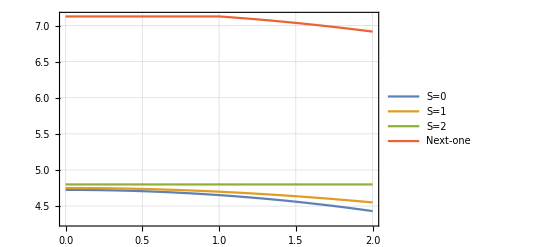

```mathematica
ListLinePlot[{e0data[[1;;21,1;;2]],e1data[[1;;21,1;;2]],e2data[[1;;21,1;;2]],e3data[[1;;21,1;;2]]},PlotLegends->{"S=0","S=1","S=2","Next-one"},PlotRange->All,Frame->True,GridLines->Automatic]
```

```mathematica
e1data//MatrixForm
```

(0. | 4.75034 | 2.
0.1 | 4.74983 | 2.
0.2 | 4.74829 | 2.
0.3 | 4.74572 | 2.
0.4 | 4.74213 | 2.
0.5 | 4.73753 | 2.
0.6 | 4.7319 | 2.
0.7 | 4.72527 | 2.
0.8 | 4.71762 | 2.
0.9 | 4.70898 | 2.
1. | 4.69935 | 2.
1.1 | 4.68874 | 2.
1.2 | 4.67715 | 2.
1.3 | 4.66459 | 2.
1.4 | 4.65108 | 2.
1.5 | 4.63663 | 2.
1.6 | 4.62124 | 2.
1.7 | 4.60493 | 2.
1.8 | 4.58771 | 2.
1.9 | 4.5696 | 2.
2. | 4.5506 | 2.)

```mathematica
e2data//MatrixForm
```

(0. | 4.8 | 6.
0.1 | 4.8 | 6.
0.2 | 4.8 | 6.
0.3 | 4.8 | 6.
0.4 | 4.8 | 6.
0.5 | 4.8 | 6.
0.6 | 4.8 | 6.
0.7 | 4.8 | 6.
0.8 | 4.8 | 6.
0.9 | 4.8 | 6.
1. | 4.8 | 6.
1.1 | 4.8 | 6.
1.2 | 4.8 | 6.
1.3 | 4.8 | 6.
1.4 | 4.8 | 6.
1.5 | 4.8 | 6.
1.6 | 4.8 | 6.
1.7 | 4.8 | 6.
1.8 | 4.8 | 6.
1.9 | 4.8 | 6.
2. | 4.8 | 6.)

```mathematica
e3data//MatrixForm
```

(0. | 7.12614 | 2.
0.1 | 7.12614 | 2.
0.2 | 7.12614 | 2.
0.3 | 7.12614 | 2.
0.4 | 7.12614 | 2.
0.5 | 7.12614 | 2.
0.6 | 7.12614 | 2.
0.7 | 7.12614 | 2.
0.8 | 7.12614 | 2.
0.9 | 7.12614 | 2.
1. | 7.12614 | 2.
1.1 | 7.1109 | 2.
1.2 | 7.09433 | 2.
1.3 | 7.07643 | 2.
1.4 | 7.05725 | 2.
1.5 | 7.0368 | 2.
1.6 | 7.01512 | 2.
1.7 | 6.99224 | 2.
1.8 | 6.96819 | 2.
1.9 | 6.94301 | 2.
2. | 6.91672 | 2.)

```mathematica
jj1 = Table[{e0data[[i,1]],(e2data[[i,2]]-e1data[[i,2]])/2},{i,1,Dimensions[e0data][[1]]}]
```

{{0.,0.0248288},{0.1,0.0250855},{0.2,0.0258557},{0.3,0.0271385},{0.4,0.0289328},{0.5,0.0312371},{0.6,0.0340494},{0.7,0.0373672},{0.8,0.0411877},{0.9,0.0455077},{1.,0.0503234},{1.1,0.0556309},{1.2,0.0614259},{1.3,0.0677034},{1.4,0.0744586},{1.5,0.0816861},{1.6,0.0893802},{1.7,0.097535},{1.8,0.106144},{1.9,0.115202},{2.,0.124701}}

```mathematica
jj2 = Table[{e0data[[i,1]],((e0data[[i,2]])/3 ) +((e2data[[i,2]])/6)-((e1data[[i,2]])/2) },{i,1,Dimensions[e0data][[1]]}]
```

{{0.,-0.000295981},{0.1,-0.000278975},{0.2,-0.000228357},{0.3,-0.000145328},{0.4,-0.0000318805},{0.5,0.000109218},{0.6,0.000274443},{0.7,0.000459537},{0.8,0.000659541},{0.9,0.000868833},{1.,0.00108117},{1.1,0.00128971},{1.2,0.00148711},{1.3,0.00166555},{1.4,0.00181676},{1.5,0.00193214},{1.6,0.00200281},{1.7,0.00201963},{1.8,0.00197333},{1.9,0.00185454},{2.,0.00165387}}

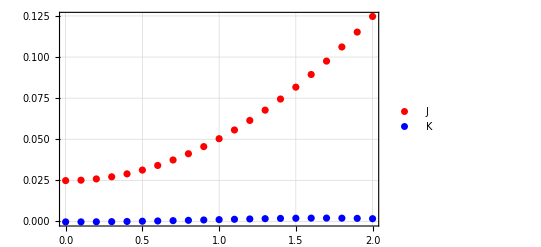

```mathematica
ListPlot[{jj1,jj2},PlotRange->Automatic,GridLines->Automatic,Frame->True,PlotLegends->Placed[{"J","K"},{Left,Center}],PlotStyle->{Red,Blue}]
```

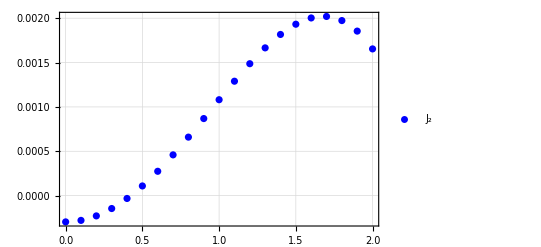

```mathematica
ListPlot[{jj2},PlotRange->Automatic,GridLines->Automatic,Frame->True,Frame->True,PlotLegends->Placed[{"J_2"},{Left,Center}],PlotStyle->Blue]
```

```mathematica
beta= Table[{e0data[[i,1]],-jj2[[i,2]]/jj1[[i,2]]},{i,1,Dimensions[e0data][[1]]}]
```

{{0.,(2 (1))/(-4.70898+1)},49,{0.8,1}}
 |  |  |  |